```mathematica
∑_(k=0)^3 ϵ^(2k)/(k!)
```

1+ϵ^2+ϵ^4/2+ϵ^6/6

```mathematica
∑_(k=0)^3 (ϵ Subscript[c, T])^k/(k!)
```

1+ϵ c_T+1/2 ϵ^2 c_T^2+1/6 ϵ^3 c_T^3

```mathematica
norm[ϵ_]=1/(√(1+ϵ^2));
Subscript[ψ, T]=norm[ϵ](1+ϵ Subscript[c, T]);
Subscript[ψ, abcd]=α Subscript[c, b0]+β Subscript[c, a];
ψ=Expand[Subscript[ψ, T] Subscript[ψ, abcd]];
B[t_]={{t,ⅈ √(1-t^2)},{ⅈ  √(1-t^2),t}};
```

#### Extra beamsplitter in Rail 2

```mathematica
{Subscript[c, b0],Subscript[c, d0]}=B[Subscript[t, 4]].{Subscript[c, b],Subscript[c, d]};
```

#### Modes T and a mix at the first beamsplitter:

```mathematica
{Subscript[c, T],Subscript[c, a]}=B[Subscript[t, 1]].{Subscript[c, T1],Subscript[c, a1]};
```

#### Nonlinear phase gate

```mathematica
{Subscript[A, 0],Subscript[A, 1],Subscript[A, 2]}=CoefficientList[Expand[ψ],Subscript[c, T1]];
ψ=Subscript[A, 0]+Subscript[A, 1] Subscript[c, T1]+ⅇ^(ⅈ X)Subscript[A, 2] Subscript[c, T1]^2;
```

```mathematica
(*{Subscript[A, 0],Subscript[A, 1],Subscript[A, 2],Subscript[A, 3],Subscript[A, 4]}=CoefficientList[Expand[ψ],Subscript[c, T1]];
ψ=Subscript[A, 0]+Subscript[A, 1] Subscript[c, T1]+ⅇ^(ⅈ π/2)Subscript[A, 2] Subscript[c, T1]^2+0.720808055789109 ⅇ^(ⅈ 3.292139505690955)  Subscript[A, 3] Subscript[c, T1]^3+0.4550849490325603 ⅇ^(ⅈ 3.336228752377668)  Subscript[A, 4] Subscript[c, T1]^4;*)
```

#### Modes T1 and b mix at the second beamsplitter:

```mathematica
{Subscript[c, T1],Subscript[c, b]}=B[Subscript[t, 2]].{Subscript[c, T2],Subscript[c, b1]};
```

#### Modes T2 and c mix at the third beamsplitter:

```mathematica
{Subscript[c, T2],Subscript[c, c]}=B[Subscript[t, 3]].{Subscript[c, T3],Subscript[c, c1]};
```

### Project onto the state where we have 0,0,1 photons in the modes ‘a1’, ‘b1’ and ‘c1’ respectively The ‘1’ in the labels of the modes denotes that they are outputs modes of beamsplitters

```mathematica
Collect[FullSimplify[-1/((√(1-Subscript[t, 3]^2))/(√(1+ ϵ^2)))CoefficientList[Expand[ψ],{Subscript[c, a1],Subscript[c, b1],Subscript[c, c1],Subscript[c, d]}][[1,1,2,1]]],{α,β}]
```

β (√(1-t_1^2) t_2+2 ⅇ^(ⅈ X) ϵ c_T3 t_1 √(1-t_1^2) t_2^2 t_3)+α (√(1-t_2^2) t_4+2 ϵ c_T3 t_1 t_2 √(1-t_2^2) t_3 t_4)

#### Calculating P_S=ψ'ψ'

```mathematica
prefactor=(1-Subscript[t, 3]^2)/(1+ ϵ^2);
```

```mathematica
clist=CoefficientList[FullSimplify[ComplexExpand[(β ⅇ^(-ⅈ ϕ) (Subscript[r, 1] Subscript[t, 2]+2 ⅇ^(-ⅈ X) ϵ Subscript[c, T3] Subscript[t, 1] Subscript[r, 1] Subscript[t, 2]^2 Subscript[t, 3])+α (Subscript[r, 2] Subscript[t, 4]+2 ϵ Subscript[c, T3] Subscript[t, 1] Subscript[t, 2] Subscript[r, 2] Subscript[t, 3] Subscript[t, 4]))(β ⅇ^(ⅈ ϕ) (Subscript[r, 1] Subscript[t, 2]+2 ⅇ^(ⅈ X) ϵ Subscript[c, T3] Subscript[t, 1] Subscript[r, 1] Subscript[t, 2]^2 Subscript[t, 3])+α (Subscript[r, 2] Subscript[t, 4]+2 ϵ Subscript[c, T3] Subscript[t, 1] Subscript[t, 2] Subscript[r, 2] Subscript[t, 3] Subscript[t, 4]))]],Subscript[c, T3]];
clist2=Simplify[CoefficientList[clist[[1]]+clist[[3]],{α,β}]];
```

```mathematica
clist2[[3,1]]
```

r_2^2 (1+4 ϵ^2 t_1^2 t_2^2 t_3^2) t_4^2

```mathematica
clist2[[1,3]]
```

r_1^2 t_2^2 (1+4 ϵ^2 t_1^2 t_2^2 t_3^2)

```mathematica
clist2[[2,2]]
```

2 r_1 r_2 t_2 (Cos[ϕ]+4 ϵ^2 Cos[X+ϕ] t_1^2 t_2^2 t_3^2) t_4

```mathematica
ClearAll[ϵ,t1,t2,t3,t4]
Subscript[P, S][α_,ϵ_,ϕ_,X_,t1_,t2_,t3_,t4_]=0.18((1-t3^2)/(1+ϵ^2))((1+(ϵ 2 t1 t2 t3)^2)(α^2(√(1-t2^2) t4)^2+(1-α^2)(√(1-t1^2) t2)^2)+2 √(1-t1^2)√(1-t2^2)t2 t4 α √(1-α^2)(Cos[ϕ]+(ϵ 2t1 t2 t3)^2 Cos[ϕ+X]));
```

```mathematica
N[ Subscript[P, S][1/(√2),1/(√2),0,π/2,1/2^(1/3),1/2^(1/3),1/2^(1/3),1/2^(1/3)]]
```

0.025878

#### Verification: previous results in klm-calc-v4

```mathematica
Plot3D[N[Subscript[P, S][α,0.1,ϕ,π/2,1/2^(1/3),1/2^(1/3),1/2^(1/3),1/2^(1/3)]],{α,0,1},{ϕ,0,2π}]
```

-Graphics3D-

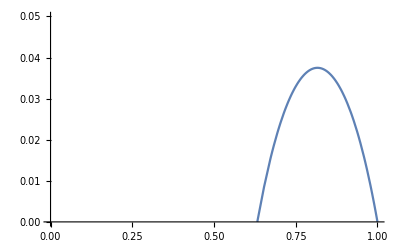

```mathematica
Plot[ Subscript[P, S][1/(√2),1/(√2),0,π/2,t,1/(√(2-t^2)),(√(2-t^2))/(2t),1],{t,0,1},PlotRange->{0,0.05},GridLines->{{0,√(2/5),1/2^(1/3),0.8164965731998214,1}, {0,0.1}}]
```

```mathematica
FindMaximum[Subscript[P, S][1/(√2),1/(√2),0,π/2,t,1/(√(2-t^2)),(√(2-t^2))/(2t),1],{t,1/2^(1/3)}]
```

{0.0375,{t→0.816497}}

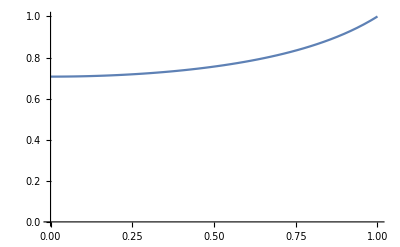

```mathematica
Plot[1/(√(2-t^2)),{t,0,1},PlotRange->{0,1},GridLines->{{0,√(2/5),1/2^(1/3),0.8164965731998214,1}, {0,1}}]
```

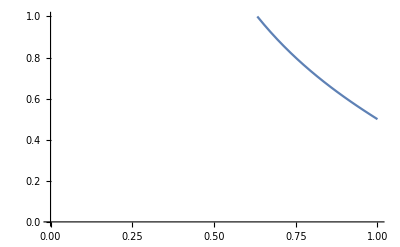

```mathematica
Plot[(√(2-t^2))/(2t),{t,0,1},PlotRange->{0,1},GridLines->{{0,√(2/5),1/2^(1/3),0.8164965731998214,1}, {0,1}}]
```

### Fidelity

#### Calculations for Fidelity

```mathematica
ClearAll[α,ϵ,ϕ,X,t1,t2,t3,t4]
clistw=CoefficientList[ComplexExpand[(√(1-α^2) ⅇ^(-ⅈ ϕ)(1+ ⅇ^(-ⅈ X) ϵ Subscript[c, T3] )+α(1+ ϵ Subscript[c, T3]))(√(1-α^2) ⅇ^(ⅈ ϕ) (1+ ⅇ^(ⅈ X) ϵ Subscript[c, T3] )+α (1+ ϵ Subscript[c, T3]))],Subscript[c, T3]];
normw=1/√FullSimplify[clistw[[1]]+clistw[[3]]];
```

```mathematica
clisth=CoefficientList[ComplexExpand[(√(1-α^2) ⅇ^(-ⅈ ϕ) (√(1-t1^2) t2+2 ⅇ^(-ⅈ X) ϵ Subscript[c, T3] t1 √(1-t1^2) t2^2 t3)+α (√(1-t2^2) t4+2 ϵ Subscript[c, T3] t1 t2 √(1-t2^2) t3 t4))(√(1-α^2) ⅇ^(ⅈ ϕ) (√(1-t1^2) t2+2 ⅇ^(ⅈ X) ϵ Subscript[c, T3] t1 √(1-t1^2) t2^2 t3)+α (√(1-t2^2) t4+2 ϵ Subscript[c, T3] t1 t2 √(1-t2^2) t3 t4))],Subscript[c, T3]];
normh=1/√FullSimplify[clisth[[1]]+clisth[[3]],0≤t1≤ 1&&0≤t2≤ 1&&0≤t3≤ 1&&0≤t4≤ 1];
```

```mathematica
clistwh=FullSimplify[CoefficientList[ComplexExpand[(√(1-α^2) ⅇ^(-ⅈ ϕ) (√(1-t1^2) t2+2 ⅇ^(-ⅈ X) ϵ Subscript[c, T3] t1 √(1-t1^2) t2^2 t3)+α (√(1-t2^2) t4+2 ϵ Subscript[c, T3] t1 t2 √(1-t2^2) t3 t4))(√(1-α^2)ⅇ^(ⅈ ϕ) (1+ ⅇ^(ⅈ X) ϵ Subscript[c, T3] )+α (1+ ϵ Subscript[c, T3]))],Subscript[c, T3]],0≤t1≤ 1&&0≤t2≤ 1&&0≤t3≤ 1&&0≤t4≤ 1&&0≤α≤ 1];
clistwh[[1]]+clistwh[[3]]
```

-√(1-t1^2) t2 (-1+α^2)+ⅇ^(-ⅈ ϕ) t2 α √((-1+t1^2) (-1+α^2))+t4 α (√(1-t2^2) α+ⅇ^(ⅈ ϕ) √((-1+t2^2) (-1+α^2)))+2 t1 t2 t3 (-√(1-t1^2) t2 (-1+α^2)+ⅇ^(-ⅈ (X+ϕ)) t2 α √((-1+t1^2) (-1+α^2))+t4 α (√(1-t2^2) α+ⅇ^(ⅈ (X+ϕ)) √((-1+t2^2) (-1+α^2)))) ϵ^2

```mathematica
Fcalc[α_,ϵ_,ϕ_,X_,t1_,t2_,t3_,t4_]=Abs[normh normw (-√(1-t1^2) t2 (-1+α^2)+ⅇ^(-ⅈ ϕ) t2 α √((-1+t1^2) (-1+α^2))+t4 α (√(1-t2^2) α+ⅇ^(ⅈ ϕ) √((-1+t2^2) (-1+α^2)))+2 t1 t2 t3 (-√(1-t1^2) t2 (-1+α^2)+ⅇ^(-ⅈ (X+ϕ)) t2 α √((-1+t1^2) (-1+α^2))+t4 α (√(1-t2^2) α+ⅇ^(ⅈ (X+ϕ)) √((-1+t2^2) (-1+α^2)))) ϵ^2)]^2;
```

#### Code

```mathematica
norm1[α_,ϵ_,ϕ_,X_,t1_,t2_,t3_,t4_]=1/(√((t4^2 α^2+t2^2 (1-(1+t4^2) α^2+t1^2 (-1+α^2))) (1+4 t1^2 t2^2 t3^2 ϵ^2)+2 √(1-t1^2) t2 √(1-t2^2) t4 α √(1-α^2) (Cos[ϕ]+4 t1^2 t2^2 t3^2 ϵ^2 Cos[X+ϕ])));
norm2[α_,ϵ_,ϕ_,X_,t1_,t2_,t3_,t4_]=1/(√(1+ϵ^2+2 α √(1-α^2) (Cos[ϕ]+ϵ^2 Cos[X+ϕ])));
F[α_,ϵ_,ϕ_,X_,t1_,t2_,t3_,t4_]=Abs[norm1[α,ϵ,ϕ,X,t1,t2,t3,t4] norm2[α,ϵ,ϕ,X,t1,t2,t3,t4]( (α+ⅇ^(-ⅈ ϕ) √(1-α^2)) (√(1-t2^2) t4 α+ⅇ^(ⅈ ϕ) √(1-t1^2) t2 √(1-α^2))+2 t1 t2 t3 (α+ⅇ^(-ⅈ (X+ϕ)) √(1-α^2)) (√(1-t2^2) t4 α+ⅇ^(ⅈ (X+ϕ)) √(1-t1^2) t2 √(1-α^2)) ϵ^2)]^2;
```

```mathematica
Q[α_,ϵ_,ϕ_,X_,t1_,t2_,t3_,t4_]=(F[α,ϵ,ϕ,X,t1,t2,t3,t4])/1 Subscript[P, S][α,ϵ,ϕ,X,t1,t2,t3,t4];
```

```mathematica
fp=Manipulate[GraphicsRow[{Plot3D[F[1/(√2),1,0,π/2,t1,t2,t3,0.9999965078753951],{t1,0,1},{t2,0,1},ImageSize->Full,PlotLabel->"F",PlotRange->{0,1},AxesLabel->Automatic,Mesh-> None,PlotStyle->Opacity[0.7]],Plot3D[Subscript[P, S][1/(√2),1,0,π/2,t1,t2,t3,0.9999965078753951],{t1,0,1},{t2,0,1},ImageSize->Full,PlotLabel->"P_S",PlotRange->{0,0.1},AxesLabel->Automatic,Mesh-> None,PlotStyle->Opacity[0.7]]}],{t3,0,1,Appearance-> "Open"}]
```

```mathematica
Export["fp.gif", fp,"DisplayDurations"->0.1,"AnimationRepetitions" ->  Infinity]
```

fp.gif

```mathematica
q=Manipulate[Plot3D[ F[1/(√2),1/(√2),0,π/2,t1,t2,t3,1] Subscript[P, S][1/(√2),1/(√2),0,π/2,t1,t2,t3,1],{t1,0,1},{t2,0,1},ImageSize->Scaled[0.4],PlotLabel->"Q",PlotRange->{0,0.1},AxesLabel->Automatic,Mesh-> None,PlotStyle->Opacity[0.7]],{t3,0,1,Appearance-> "Open"}]
```

```mathematica
Export["q.gif", q,"DisplayDurations"->0.1,"AnimationRepetitions" ->  Infinity]
```

$Aborted

```mathematica
ClearAll[t1,t2,t3,t4,α,ϵ,ϕ,X]
α=1/(√2);
ϵ=1;
ϕ=0;
X=π/2;
{val,subs}=FindMaximum[{ Fcalc[α,ϵ,ϕ,X,t1,t2,t3,t4]Subscript[P, S][α,ϵ,ϕ,X,t1,t2,t3,t4],0≤ t1≤ 1&&0≤t2≤ 1&&0≤t3≤ 1&&0≤t4≤ 1},{t1,1/2^(1/3)},{t2,1/2^(1/3)},{t3,1/2^(1/3)},{t4,1/2^(1/3) }]
```

{0.0599999,{t1→0.0348592,t2→0.70732,t3→0.0246568,t4→0.999998}}

```mathematica
{val,subs}=FindMaximum[{ F[α,ϵ,ϕ,X,t1,t2,t3,t4]Subscript[P, S][α,ϵ,ϕ,X,t1,t2,t3,t4],0≤ t1≤ 1&&0≤t2≤ 1&&0≤t3≤ 1&&0≤t4≤ 1},{t1,1/2^(1/3)},{t2,1/2^(1/3)},{t3,1/2^(1/3)},{t4,1/2^(1/3) }]
```

{0.0599999,{t1→0.0348592,t2→0.70732,t3→0.0246568,t4→0.999998}}

```mathematica
N[Fcalc[1/(√2),1/(√2),0,π/2,1/2^(1/3),1/2^(1/3),1/2^(1/3),1/2^(1/3)]]
```

1.

```mathematica
N[Subscript[P, S][1/(√2),1/(√2),0,π/2,1/2^(1/3),1/2^(1/3),1/2^(1/3),1/2^(1/3)]]
```

0.025878

```mathematica
ReplaceAll[Fcalc[α,ϵ,ϕ,X,t1,t2,t3,t4],subs]
```

0.667477

```mathematica
ReplaceAll[Subscript[P, S][α,ϵ,ϕ,X,t1,t2,t3,t4],subs]
```

0.0898905

```mathematica
ReplaceAll[2 t1 t2 t3,subs]
```

0.0012159

```mathematica
Plot3D[{ReplaceAll[Subscript[P, S][α,1,ϕ,π/2,t1,t2,t3,t4],subs],0.0452050731077118},{ϕ,0,1},{α,0,1},ImageSize->Scaled[0.5],AxesLabel->Automatic,Mesh-> None,ImageSize->Full,PlotStyle-> {Opacity[1],Opacity[0.2]},PlotRange-> Full,LabelStyle->{FontSize->15,FontFamily->"Cambria", Black},PlotLabel->"P_S (with t_k optimized for α=β=1/(√2),ϵ=1, X=π/2)"]
```

-Graphics3D-

```mathematica
ClearAll[t1,t2,t3,t4,α,ϵ,ϕ,X]
α=1/(√2);
ϵ=1/(√2);
ϕ=0;
X=π/2;
{val,subs}=FindMaximum[{F[α,ϵ,ϕ,X,t1,t2,t3,t4] Subscript[P, S][α,ϵ,ϕ,X,t1,t2,t3,t4],0≤ t1<1&&0≤t2<1&&0≤t3<1&&0≤t4<1},{t1,0.5},{t2,0.5},{t3,0.5},{t4,0.5}]
```

{0.533333,{t1→0.00132481,t2→0.707107,t3→0.000958844,t4→1.}}

```mathematica
ReplaceAll[F[α,ϵ,ϕ,X,t1,t2,t3,1],subs]
```

0.800001

```mathematica
ReplaceAll[Subscript[P, S][α,ϵ,ϕ,X,t1,t2,t3,1],subs]
```

0.666665

```mathematica
ReplaceAll[2 t1 t2 t3,subs]
```

1.79646×10^-6

```mathematica
Plot3D[{ReplaceAll[Subscript[P, S][α,1/(√2),ϕ,π/2,t1,t2,t3,t4],subs],0.0452050731077118},{ϕ,0,1},{α,0,1},ImageSize->Scaled[0.5],AxesLabel->Automatic,Mesh-> None,ImageSize->Full,PlotStyle-> {Opacity[1],Opacity[0.2]},PlotRange-> Full,LabelStyle->{FontSize->15,FontFamily->"Cambria", Black},PlotLabel->"P_S (with t_k optimized for α=β=ϵ=1/(√2), X=π/2)"]
```

-Graphics3D-

#### Rough Work

```mathematica
N[F[1/(√2),1/(√2),0,π/2,1/2^(1/3),1/2^(1/3),1/2^(1/3),1/2^(1/3)]]
```

1.

```mathematica
ψ1=(α+β)A+ϵ(α+ⅇ^(ⅈ X)β)B
ψ2=(α √(1-t2^2)t4+β √(1-t1^2)t2)A+ϵ 2  t1 t2 t3(α √(1-t2^2)t4+ⅇ^(ⅈ X)β √(1-t1^2)t2)B
```

A (α+β)+B (α+ⅇ^(ⅈ X) β) ϵ

A (√(1-t2^2) t4 α+√(1-t1^2) t2 β)+2 B t1 t2 t3 (√(1-t2^2) t4 α+ⅇ^(ⅈ X) √(1-t1^2) t2 β) ϵ

```mathematica
Collect[FullSimplify[(α √(1-t2^2)t4+ⅇ^(-ⅈ ϕ)√(1-α^2)√(1-t1^2)t2)(α √(1-t2^2)t4+ⅇ^(ⅈ ϕ)√(1-α^2)√(1-t1^2)t2)+(ϵ 2  t1 t2 t3)^2(α √(1-t2^2)t4+ⅇ^(-ⅈ (X+ϕ))√(1-α^2)√(1-t1^2)t2)(α √(1-t2^2)t4+ⅇ^(ⅈ (X+ϕ))√(1-α^2)√(1-t1^2)t2)],1+(ϵ 2 t1 t2 t3)^2]
```

(t4^2 α^2+t2^2 (1-(1+t4^2) α^2+t1^2 (-1+α^2))) (1+4 t1^2 t2^2 t3^2 ϵ^2)+2 √(1-t1^2) t2 √(1-t2^2) t4 α √(1-α^2) (Cos[ϕ]+4 t1^2 t2^2 t3^2 ϵ^2 Cos[X+ϕ])

```mathematica
FullSimplify[(α+√(1-α^2)ⅇ^(-ⅈ ϕ))(α+√(1-α^2)ⅇ^(ⅈ ϕ))+ϵ^2(α+ⅇ^(-ⅈ X)√(1-α^2)ⅇ^(-ⅈ ϕ))(α+ⅇ^(ⅈ X)√(1-α^2)ⅇ^(ⅈ ϕ))]
```

1+ϵ^2+2 α √(1-α^2) (Cos[ϕ]+ϵ^2 Cos[X+ϕ])

```mathematica
FullSimplify[(α+√(1-α^2)ⅇ^(-ⅈ ϕ))(α √(1-t2^2)t4+ⅇ^(ⅈ ϕ)√(1-α^2)√(1-t1^2)t2)+ϵ^2 2  t1 t2 t3(α+ⅇ^(-ⅈ X)√(1-α^2)ⅇ^(-ⅈ ϕ))(α √(1-t2^2)t4+ⅇ^(ⅈ (X+ϕ))√(1-α^2)√(1-t1^2)t2)]
```

(α+ⅇ^(-ⅈ ϕ) √(1-α^2)) (√(1-t2^2) t4 α+ⅇ^(ⅈ ϕ) √(1-t1^2) t2 √(1-α^2))+2 t1 t2 t3 (α+ⅇ^(-ⅈ (X+ϕ)) √(1-α^2)) (√(1-t2^2) t4 α+ⅇ^(ⅈ (X+ϕ)) √(1-t1^2) t2 √(1-α^2)) ϵ^2

```mathematica
t1=(√6)/3;
t2=(√3)/2;
t3=1/(√2);
t4=1;
ϕ=0;
X=π/2;ϵ=1; 
α=1/(√2);
(((√(1-t3^2))^2(1+(ϵ 2 t1 t2 t3)^2))/(1+ϵ^2))(α^2(√(1-t2^2) t4)^2+(1-α^2)(√(1-t1^2) t2)^2+2 √(1-t1^2)√(1-t2^2)t2 t4 α √(1-α^2)(Cos[ϕ]+(ϵ 2t1 t2 t3)^2 Cos[ϕ+X]))
```

1/4

```mathematica
(.18)^2 10^-4
```

3.24×10^-6

URLFetch::invhttp: A library error occurred. The raw details are: "libcurl error (28): Send failure: Connection was aborted"

CloudObjectInformation::cloudnf: No CloudObject found at the given address

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

Part::pspec1: Part specification FileByteCount is not applicable.